```mathematica
ClearAll["Global‘*"]
Clear[minx,miny,maxx,maxy]
minx = -2;
miny = -2;
maxx = 2;
maxy = 2;
```

```mathematica
Clear[sol,x,y,t]
sol[x0_,y0_] := NDSolve[
{x'[t] == (0 + 1)*x[t] + 3*y[t],
y'[t]==-2*x[t] +(0 - 1)*y[t],
x[0]==x0,y[0]==y0},
{x,y},{t,-100,10}]
```

```mathematica
initialCond = Join[
Table[{x,maxy},{x,minx , maxx,0.1}],
Table[{minx , y } , {y,miny , maxy,0.1}],
Table[{x , miny},{x , minx , maxx,0.1}],
Table[{maxx, y} , {y, miny , maxy,0.1}]
];
```

InterpolatingFunction::dmval: Input value {-999.979} lies outside the range of data in the interpolating function. Extrapolation will be used.

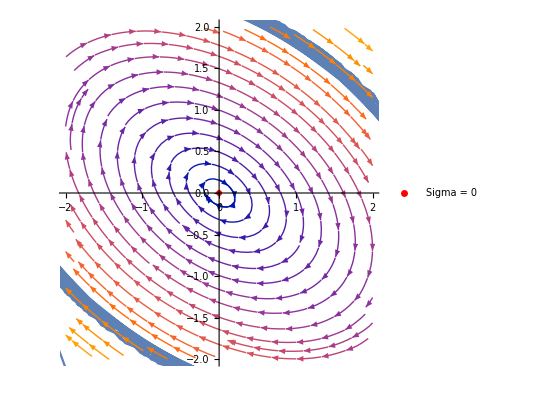

```mathematica
Show[ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[initialCond[[50,1]],initialCond[[50,2]]]],
{t,-1000,10}, PlotRange->{{minx,maxx},{miny,maxy}}],
StreamPlot[{(0 + 1)*x + 3*y,-2*x +(0 - 1)*y},{x,-2,2},{y,-2,2}],
ListPlot[{{0,0}},PlotStyle->{PointSize[0.03],Red}, PlotMarkers->{"",Large},PlotLegends->{"Sigma = 0"}]
]
```

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t], y[t]}/.sol[initialCond[[i,1]], initialCond[[i,2
]]]],{t,-100,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,1,Length[initialCond]}],
ListPlot[{{0,0}},PlotStyle->{PointSize[0.03],Red}, PlotMarkers->{"",Large},PlotLegends->{"Sigma = 0"}]
]
```

-Graphics-

```mathematica
Show[p2,StreamPlot[{(0 + 1)*x + 3*y,-2*x +(0 - 1)*y},{x,-2,2},{y,-2,2}],PlotRange->{{minx,maxx},{miny,maxy}}]
```

-Graphics-